Formal Christoffel symbols

Point and direction coordinates:

```mathematica
X={t,x,y};
V={v1,v2};
```

Definitions for a specific case (do not evaluate these cells for a purely symbolic computation):

```mathematica
z[x_,y_]:=Exp[-x^2/10];
phi[t_,x_,y_]:=2t;
a[t_,x_,y_]:=1+t;
epsilon[t_,x_,y_]:=0.8;
h[t_,x_,y_]:=1+x^2/2;
```

Finsler metric:

```mathematica
beta[x_,y_,v1_,v2_]:=v1 D[z[x1,x2],x1]+v2 D[z[x1,x2],x2]/.{x1->x,x2->y};
alpha[x_,y_,v1_,v2_]:=Sqrt[v1^2+v2^2+beta[x,y,v1,v2]^2];
omega[t_,x_,y_,v1_,v2_]:=(v1+D[z[x1,x2],x1]beta[x,y,v1,v2])Cos[phi[t,x,y]]/Sqrt[1+D[z[x1,x2],x1]^2]+(v2+D[z[x1,x2],x2]beta[x,y,v1,v2])Sin[phi[t,x,y]]/Sqrt[1+D[z[x1,x2],x2]^2]/.{x1->x,x2->y};
dz[x_,y_,v1_,v2_]:={v1,v2,beta[x,y,v1,v2]};
F[t_,x_,y_,v1_,v2_]:=alpha[x,y,v1,v2]^2/(alpha[x,y,v1,v2]^2 a[t,x,y](1-epsilon[t,x,y]^2)/(alpha[x,y,v1,v2]-epsilon[t,x,y]omega[t,x,y,v1,v2])+h[t,x,y](alpha[x,y,v1,v2]+beta[x,y,v1,v2]));
```

Coefficients of the fundamental tensor of the Lorentz-Finsler metric G=dt^2-F^2:

```mathematica
g00[t_,x_,y_,v1_,v2_]:=1-1/2D[F[t,x,y,v1,v2]^2,d,e]/.{d->0,e->0};
g10[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1+d,v2]^2,d,e]/.{d->0,e->0};
g01[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1+e,v2]^2,d,e]/.{d->0,e->0};
g20[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1,v2+d]^2,d,e]/.{d->0,e->0};
g02[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1,v2+e]^2,d,e]/.{d->0,e->0};
g11[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1+d+e,v2]^2,d,e]/.{d->0,e->0};
g22[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1,v2+d+e]^2,d,e]/.{d->0,e->0};
g12[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1+d,v2+e]^2,d,e]/.{d->0,e->0};
g21[t_,x_,y_,v1_,v2_]:=-1/2D[F[t,x,y,v1+e,v2+d]^2,d,e]/.{d->0,e->0};
g[t_,x_,y_,v1_,v2_]:={{g00[t,x,y,v1,v2],g01[t,x,y,v1,v2],g02[t,x,y,v1,v2]},{g10[t,x,y,v1,v2],g11[t,x,y,v1,v2],g12[t,x,y,v1,v2]},{g20[t,x,y,v1,v2],g21[t,x,y,v1,v2],g22[t,x,y,v1,v2]}};
ginv[t_,x_,y_,v1_,v2_]:=Inverse[g[t,x,y,v1,v2]];
```

Formal Christoffel symbols:

```mathematica
gammaMatrix=Table[1/2(Sum[ginv[t,x,y,v1,v2][[k,r]](D[g[t,x,y,v1,v2][[r,j]],X[[i]]]+D[g[t,x,y,v1,v2][[r,i]],X[[j]]]-D[g[t,x,y,v1,v2][[i,j]],X[[r]]]),{r,1,3}]),{k,3},{i,3},{j,3}];
gamma[t_,x_,y_,v1_,v2_]=gammaMatrix;
```

Solution to the ODE system given by the geodesic equations

Number of curves to be computed, number of firefronts and total time:

```mathematica
ncurves=40;
nfronts=4;
T=0.7;
fr=Take[Subdivide[T,nfronts],{2,nfronts+1}];
```

Initial conditions (firefront at t=0 is a single point):

```mathematica
X0=ConstantArray[{-0.5,0},ncurves];
V0=Table[{Cos[m(2Pi/ncurves)],Sin[m(2Pi/ncurves)]},{m,ncurves}];
dX0=Table[V0[[i,j]]/F[0,X0[[i,1]],X0[[i,2]],V0[[i,1]],V0[[i,2]]],{i,ncurves},{j,2}];
front=ListPlot[{X0[[1]]},PlotStyle->{Red,PointSize[Large]}];
front3d=ListPointPlot3D[{{X0[[1,1]],X0[[1,2]],z[X0[[1,1]],X0[[1,2]]]}},PlotStyle->{Red,PointSize[Large]}];
```

Initial conditions (firefront at t=0 is a closed curve):

```mathematica
f[s_]:={0.2Cos[s]Cos[Pi/4]-0.3Sin[s]Sin[Pi/4]-1,0.2Cos[s]Sin[Pi/4]+0.3Sin[s]Cos[Pi/4]};
X0=Table[f[m(2Pi/ncurves)],{m,ncurves}];
orth=Table[NSolve[F[0,X0[[k,1]],X0[[k,2]],v1,v2]==1&&a[0,X0[[k,1]],X0[[k,2]]](1-epsilon[0,X0[[k,1]],X0[[k,2]]]^2)/(alpha[X0[[k,1]],X0[[k,2]],v1,v2]-epsilon[0,X0[[k,1]],X0[[k,2]]]omega[0,X0[[k,1]],X0[[k,2]],v1,v2])^2(epsilon[0,X0[[k,1]],X0[[k,2]]](2dz[X0[[k,1]],X0[[k,2]],v1,v2].dz[X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]] omega[0,X0[[k,1]],X0[[k,2]],v1,v2]-alpha[X0[[k,1]],X0[[k,2]],v1,v2]^2 omega[0,X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]])-alpha[X0[[k,1]],X0[[k,2]],v1,v2]dz[X0[[k,1]],X0[[k,2]],v1,v2].dz[X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]])+2dz[X0[[k,1]],X0[[k,2]],v1,v2].dz[X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]]-h[0,X0[[k,1]],X0[[k,2]]](dz[X0[[k,1]],X0[[k,2]],v1,v2].dz[X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]]/alpha[X0[[k,1]],X0[[k,2]],v1,v2]+beta[X0[[k,1]],X0[[k,2]],f'[k(2Pi/ncurves)][[1]],f'[k(2Pi/ncurves)][[2]]])==0&&Det[{{v1,f'[k(2Pi/ncurves)][[1]]},{v2,f'[k(2Pi/ncurves)][[2]]}}]>0,{v1,v2},Reals],{k,ncurves}];
dX0=Table[{v1,v2}/.orth[[i,1]],{i,ncurves}];
front=ParametricPlot[f[s],{s,0,2Pi},PlotStyle->Red];
front3d=ParametricPlot3D[{f[s][[1]],f[s][[2]],z[f[s][[1]],f[s][[2]]]},{s,0,2Pi},PlotStyle->Red];
```

Solution:

```mathematica
sol=Table[NDSolve[{x''[t]==-gamma[t,x[t],y[t],x'[t],y'[t]][[2,1,1]]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,1,1]]x'[t]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[2,1,j]]X[[j]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,1,j]]X[[j]]'[t]x'[t],{j,2,3}]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[2,i,1]]X[[i]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,i,1]]X[[i]]'[t]x'[t],{i,2,3}]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[2,i,j]]X[[i]]'[t]X[[j]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,i,j]]X[[i]]'[t]X[[j]]'[t]x'[t],{i,2,3},{j,2,3}],y''[t]==-gamma[t,x[t],y[t],x'[t],y'[t]][[3,1,1]]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,1,1]]y'[t]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[3,1,j]]X[[j]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,1,j]]X[[j]]'[t]y'[t],{j,2,3}]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[3,i,1]]X[[i]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,i,1]]X[[i]]'[t]y'[t],{i,2,3}]+Sum[-gamma[t,x[t],y[t],x'[t],y'[t]][[3,i,j]]X[[i]]'[t]X[[j]]'[t]+gamma[t,x[t],y[t],x'[t],y'[t]][[1,i,j]]X[[i]]'[t]X[[j]]'[t]y'[t],{i,2,3},{j,2,3}],x[0]==X0[[k,1]],y[0]==X0[[k,2]],x'[0]==dX0[[k,1]],y'[0]==dX0[[k,2]]},{x,y},{t,0,T},Method->{"EquationSimplification"->"Residual"}],{k,ncurves}];
xfr=Table[Flatten[x[fr]/.sol,1][[j,i]],{i,nfronts},{j,ncurves}];
yfr=Table[Flatten[y[fr]/.sol,1][[j,i]],{i,nfronts},{j,ncurves}];
xyfr=Table[{xfr[[i,j]],yfr[[i,j]]},{i,nfronts},{j,ncurves}];
xyzfr=Table[{xfr[[i,j]],yfr[[i,j]],z[xfr[[i,j]],yfr[[i,j]]]},{i,nfronts},{j,ncurves}];
```

Graphic representation in 2D:

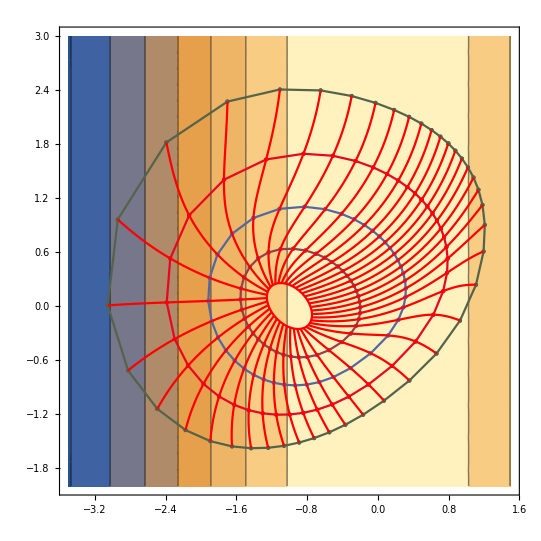

```mathematica
contour=ContourPlot[z[x,y],{x,-3.5,1.5},{y,-2,3}];
tfront=Table[ListPlot[Join[xyfr[[i]],{xyfr[[i,1]]}],PlotStyle->{PointSize[Medium],ColorData[i,"ColorList"]},Joined->True,Mesh->Full],{i,nfronts}];
fig=ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,T},PlotStyle->Red]];
Show[contour,front,tfront,fig,PlotRange->All,AspectRatio->Automatic]
```

Graphic representation in 3D:

```mathematica
surface=Plot3D[z[x,y],{x,-3.5,1.5},{y,-2,3}];
tfront3d=Table[ListPointPlot3D[xyzfr[[i]],PlotStyle->{PointSize[Large],ColorData[i,"ColorList"]}],{i,nfronts}];
fig3d=ParametricPlot3D[Evaluate[{x[t],y[t],z[x[t],y[t]]}/.sol ],{t,0,T},PlotStyle->Red];
Show[surface,front3d,tfront3d,fig3d,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-